## Kapitola 10 - RBF síť a Iris data

Demonstrace použití RBF sítě na datech z databáze UCI.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
<<NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm];
```

## Import dat

### Načtení dat ze souboru

Nastavíme si pracovní adresář na ten, kde máme uložen aktuální notebook, načítaná data musejí být ve stejném adresáři.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Dokumenty\ŠKOLA\ČVUT\BP\BP_Neuron

```mathematica
data=Import["iris.data"];
```

### Načtení dat přímo z internetu

Jiná možnost je importovat data přímo z internetu - příklad pro UCI databázi (stejná data jako v předchozím příkladu - načtení dat ze souboru).

```mathematica
data=Import["http://ftp.ics.uci.edu/pub/machine-learning-databases/iris/iris.data"];
```

## Předzpracování dat

Předzpravování dat provedeme pomocí stejného postupu, který je popsán v kapitole 5 - Dopředná síť a Iris data.

```mathematica
data2=Drop[data,-1];
inData=data2[[All,1;;4]];(*vstupní parametry*)
outDataTmp=data2[[All,5]];(*výstupní parametr*)
outVal=Tally[outDataTmp][[All,1]];
encode=MapIndexed[#1->Normal[SparseArray[#2->1,{Length[outVal]}]]&,outVal];
outData=Flatten[outDataTmp]/.encode;
```

## Zpracování dat neuronovou sítí

Inicializace sítě - zadáme trénovací množinu, rozdělenou na vstupní a výstupní data, počet neuronů, případně můžeme zadat i aktivační funkci neuronu. Počet neuronů se zadává jako kladné celé číslo.

Vytvořenou síť si uložíme do proměnné "net".

```mathematica
net=InitializeRBFNet[inData,outData,4,Neuron->Sigmoid]
```

RBFNet[{{w1, λ, w2}, χ},{Neuron → Sigmoid, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 5, 3, 19, 34, 21.0187497}, OutputNonlinearity → None, NumberOfInputs → 4}]

Můžeme si nechat zobrazit nějaké další informace o vytvořené síti.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-5-3 at 19:34. The network has 4 inputs and 3 outputs.  It consists of 4 basis functions of Sigmoid type. The network has a linear submodel.

Natrénujeme síť pomocí funkce "NeuralFit", které zadáme naší síť (proměnná "net"), trénovací množinu ("inData" a "outData") a počet učících kroků.

Funkce NeuralFit vyprodukuje naučenou síť a záznam o průběhu učení (může se hodit) - obě tyto návratové hodnoty si ukládáme (do proměnné "net2" a "record").

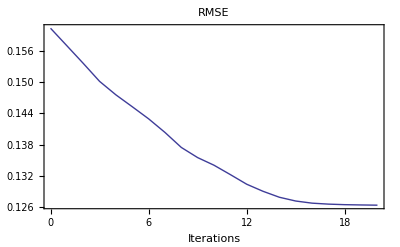

```mathematica
{net2,record}=NeuralFit[net,inData,outData,20];
```

Máme síť naučenou a můžeme se podívat na to, jak odpovídala během učení. Síť má 3 výstupy, proto následující příkaz vyprodukuje 3 grafy. Kadždý graf ukazuje počet správně a špatně klasifikovaných dat dané třídy v průběhu učení.

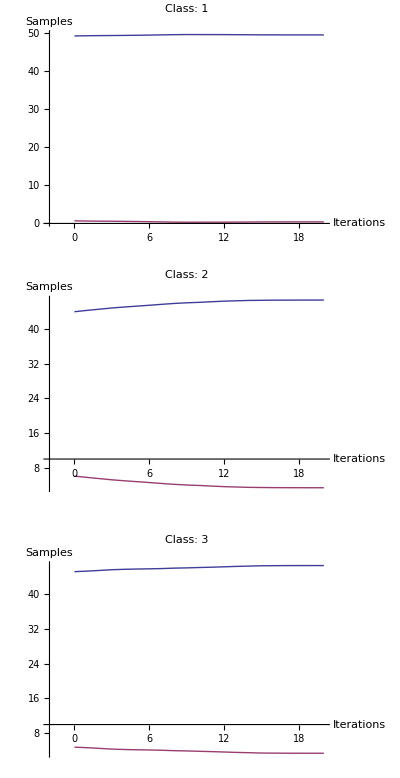

```mathematica
NetPlot[record,inData,outData,DataFormat->ClassPerformance]
```

Můžeme se podívat na klasifikaci pomocí "data/model" diagramu. Graf je interaktivní - pomocí myši ho můzeme otáčet, posouvat (Shift + myš) a zoomovat (Ctrl + myš). Čím víšší hodnoty jsou na diagonále, tím vyšší je úspěšnost klasifikace.

```mathematica
NetPlot[net2,inData,outData,DataFormat->BarChart]
```

-Graphics3D-

Síť je možné si nechat symbolicky vyhodnotit - pro větší sítě je to ale už zcela nepřehledné, nicméně aktivační funkce tam zcela jistě poznáte.

Síť funguje v Mathematice jako klasická funkce, takže ji můžeme dávat parametry - včetně symbolů.

```mathematica
net2[{x1,x2,x3,x4}]
```

{-1.17046+1.31477/(1+ⅇ^(0.361177 (-5.59364+x1)^2+0.361177 (-2.48891+x2)^2+0.361177 (-5.91684+x3)^2+0.361177 (-2.32015+x4)^2))-0.171248/(1+ⅇ^(2.9618 (-5.52981+x1)^2+2.9618 (-3.35365+x2)^2+2.9618 (-4.91668+x3)^2+2.9618 (-1.08148+x4)^2))+94.3135/(1+ⅇ^(0.17225 (-5.39172+x1)^2+0.17225 (-2.3138+x2)^2+0.17225 (-3.30242+x3)^2+0.17225 (-0.621529+x4)^2))-94.4704/(1+ⅇ^(0.173611 (-5.45451+x1)^2+0.173611 (-2.30961+x2)^2+0.173611 (-3.3057+x3)^2+0.173611 (-0.618115+x4)^2))+0.431937 x1+0.0407412 x2-0.278296 x3-0.249993 x4,8.50761-5.36592/(1+ⅇ^(0.361177 (-5.59364+x1)^2+0.361177 (-2.48891+x2)^2+0.361177 (-5.91684+x3)^2+0.361177 (-2.32015+x4)^2))+3.39149/(1+ⅇ^(2.9618 (-5.52981+x1)^2+2.9618 (-3.35365+x2)^2+2.9618 (-4.91668+x3)^2+2.9618 (-1.08148+x4)^2))-339.207/(1+ⅇ^(0.17225 (-5.39172+x1)^2+0.17225 (-2.3138+x2)^2+0.17225 (-3.30242+x3)^2+0.17225 (-0.621529+x4)^2))+337.569/(1+ⅇ^(0.173611 (-5.45451+x1)^2+0.173611 (-2.30961+x2)^2+0.173611 (-3.3057+x3)^2+0.173611 (-0.618115+x4)^2))-1.39922 x1-0.0777579 x2+0.352287 x3+0.27851 x4,-6.33715+4.05115/(1+ⅇ^(0.361177 (-5.59364+x1)^2+0.361177 (-2.48891+x2)^2+0.361177 (-5.91684+x3)^2+0.361177 (-2.32015+x4)^2))-3.22024/(1+ⅇ^(2.9618 (-5.52981+x1)^2+2.9618 (-3.35365+x2)^2+2.9618 (-4.91668+x3)^2+2.9618 (-1.08148+x4)^2))+244.893/(1+ⅇ^(0.17225 (-5.39172+x1)^2+0.17225 (-2.3138+x2)^2+0.17225 (-3.30242+x3)^2+0.17225 (-0.621529+x4)^2))-243.098/(1+ⅇ^(0.173611 (-5.45451+x1)^2+0.173611 (-2.30961+x2)^2+0.173611 (-3.3057+x3)^2+0.173611 (-0.618115+x4)^2))+0.967281 x1+0.0370167 x2-0.0739906 x3-0.0285166 x4}

V následující kapitole se podíváme podrobněji na metody učení sítě.

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011. Vznikl úpravou textu Petra Chlumského.